# Block Arnoldi

A block Arnoldi scheme looks very much like the Arnoldi scheme.

## QR Script

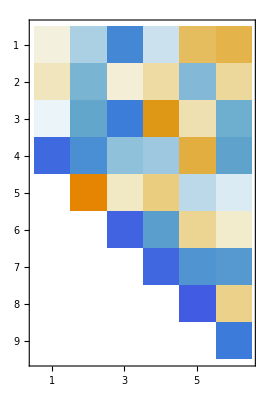

1.59326×10^-15

```mathematica
{m,b}={23,3};
A=RandomReal[{-1,1},{m,m}];
Q1= QRDecomposition[RandomReal[{-1,1},{m,b}]]⟦1⟧ᵀ;
AQ1=A.Q1;
H11=(Q1ᵀ.AQ1);
Q2=AQ1-Q1.H11;
{Q2,R21}= QRDecomposition[Q2];Q2=Q2ᵀ;
AQ2=A.Q2;
H12=(Q1ᵀ.AQ2);H22=(Q2ᵀ.AQ2);
Q3=AQ2-Q1.H12-Q2.H22;
{Q3,R32}= QRDecomposition[Q3];Q3=Q3ᵀ;
QQ2=ArrayFlatten[{{Q1,Q2}}];
QQ3=ArrayFlatten[{{Q1,Q2,Q3}}];
HH =ArrayFlatten[({{H11, H12}, {R21, H22}, {0, R32}})];
MatrixPlot[HH]
Norm[A.QQ2-QQ3.HH]
```

## Function and Testing

```mathematica
BlockArnoldiStart[A_][Q1_]:= Module[
{AQ1,H11,Q2,R21,AQ2,H12,H22,Q3,R32},
AQ1=A.Q1;
H11=(Q1ᵀ.AQ1);
Q2=AQ1-Q1.H11;
{Q2,R21}= QRDecomposition[Q2];Q2=Q2ᵀ;
AQ2=A.Q2;
H12=(Q1ᵀ.AQ2);H22=(Q2ᵀ.AQ2);
Q3=AQ2-Q1.H12-Q2.H22;
{Q3,R32}= QRDecomposition[Q3];Q3=Q3ᵀ;
{ArrayFlatten[{{Q1,Q2,Q3}}],ArrayFlatten[({{H11, H12}, {R21, H22}, {0, R32}})]}
]
```

Testing

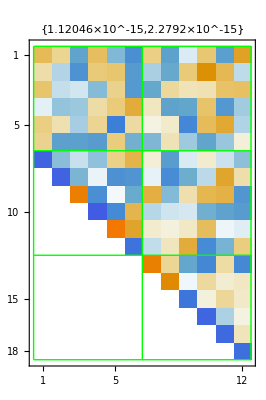

```mathematica
{m,b}={34,6};
A=RandomReal[{-1,1},{m,m}];
QIn=QRDecomposition[RandomReal[{-1,1},{m,b}]]⟦1⟧ᵀ;
{QOut,HOut}=BlockArnoldiStart[A][QIn];
MatrixPlot[HOut,
MeshStyle->Green,
Mesh->b{{0,1,2,3},{0,1,2}},
PlotLabel->Map[Norm,{QOutᵀ.QOut-IdentityMatrix[3b],A.QOut⟦All,1;;2b⟧-QOut.HOut}]]
```

## SVD Script

I think the same process should work with an SVD orthogonalization.  The reduced form should have a few more zeros. I am going to call the orthonormal basis generated U_i rather than Q_i,

```mathematica
{m,b}={23,3};
A=RandomReal[{-1,1},{m,m}];
U1= SingularValueDecomposition[RandomReal[{-1,1},{m,b}],b]⟦1⟧;
AU1=A.U1;
H11=(U1ᵀ.AU1);
U2=AU1-U1.H11;
{U2,S2,V2}= SingularValueDecomposition[U2,b];
R21=S2.V2ᵀ;
AU2=A.U2;
H12=(U1ᵀ.AU2);H22=(U2ᵀ.AU2);
U3=AU2-U1.H12-U2.H22;
{U3,S3,V3}= SingularValueDecomposition[U3,b];
R32=S3.V3ᵀ;
UU2=ArrayFlatten[{{U1,U2}}];
UU3=ArrayFlatten[{{UU2,U3}}];
VV3=ArrayFlatten[({{V2, 0}, {0, V3}})];
HQR =ArrayFlatten[({{H11, H12}, {R21, H22}, {0, R32}})];
HSVD=Chop[HQR.VV3];
Map[Dimensions,{UU3,VV3}]
TabView[{
"QR"->MatrixPlot[HQR,PlotLabel->Map[Norm,{UU3ᵀ.UU3-IdentityMatrix[3b],A.UU2-UU3.HQR}]],
"SVD"->MatrixPlot[HSVD,PlotLabel->Map[Norm,{UU3ᵀ.UU3-IdentityMatrix[3b],A.UU2.VV3-UU3.HSVD}]]
}]
```

{{23,9},{6,6}}

12

```mathematica
UU2.VV3
```

{{-0.0266975,-0.204342,-0.212202,0.231264,0.380055,0.0724341},{-0.288188,0.22483,-0.338391,-0.147764,0.0627011,0.060052},{0.234371,-0.0382777,-0.139879,-0.213007,-0.164617,0.23582},{-0.247257,-0.100733,-0.115963,0.228405,0.150272,0.156745},{-0.0967263,0.248172,-0.122975,-0.302623,-0.141982,0.0700891},{-0.32446,-0.169617,0.0133305,0.1625,-0.194204,0.125859},{-0.204682,0.0981963,0.135394,0.162035,0.0382182,0.451034},{0.4712,0.207104,0.0930834,-0.0949135,0.19534,0.0468267},{0.0200155,0.429684,0.0423086,0.00240063,0.0315321,0.306083},{0.193189,-0.314318,0.126473,0.294952,-0.169504,0.0318154},{0.029341,0.2969,-0.326171,0.429126,-0.0176492,-0.293953},{0.235402,0.101269,-0.00195305,-0.0672006,-0.0234828,-0.164515},{0.0455294,-0.197114,-0.431226,-0.135817,0.0419463,-0.228971},{-0.090775,0.208644,-0.266569,0.0906287,0.0693887,-0.247571},{0.202712,-0.0274625,-0.107579,0.00987085,-0.27023,-0.222268},{0.289209,0.204216,-0.0759678,0.342337,0.227855,0.0443182},{0.0932923,-0.126349,-0.416235,0.211184,-0.306423,0.315642},{-0.0799721,0.259861,0.230681,0.250793,0.0471538,-0.178678},{-0.122717,0.0507765,0.226429,0.332133,-0.330217,-0.189489},{-0.283887,-0.0702108,-0.000689019,-0.107005,0.445775,-0.138816},{0.171976,-0.386678,-0.0251784,0.0383747,0.252301,-0.0244285},{-0.21507,-0.0742008,0.139196,-0.143702,-0.14668,-0.351298},{-0.0773867,0.0221428,-0.262432,-0.0537674,-0.23087,0.0243432}}

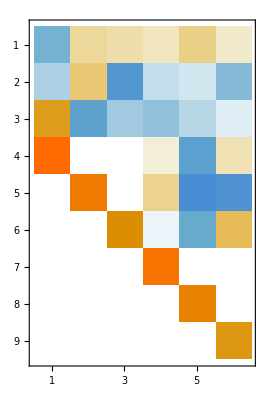

```mathematica
Map[MatrixPlot,{Chop[HH.VV3]}]
```

```mathematica
MatrixPlot[HH.VV3,PlotLabel->Map[Norm,{UU3ᵀ.UU3-IdentityMatrix[3b],A.UU2-UU3.ArrayFlatten[({{H11, H12}, {R21, H22}, {0, R32}})]}]]
```

Dot::dotsh: Tensors {{-0.5342,0.547804,0.872021,0.28862,-0.398502,0.539536},«7»,{0,0,0,1.0446,0.422026,0.638594}} and {{1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},«4»,{0,0,0,0,0,0,0.637888,0.697782,0.325882},{0,0,0,0,0,0,-0.744409,0.450216,0.493113}} have incompatible shapes.

MatrixPlot::mat0: Argument {{-0.5342,0.547804,0.872021,0.28862,-0.398502,0.539536},«7»,{0,0,0,1.0446,0.422026,0.638594}}.{{1,0,0,0,0,0,0,0,0},«7»,{«1»}} at position 1 is not a matrix.

MatrixPlot[{{-0.5342,0.547804,0.872021,0.28862,-0.398502,0.539536},{0.425522,0.0395034,0.407797,0.0938537,0.0645067,-0.131659},{-0.117346,0.250367,0.855576,-0.119134,-0.277479,-0.197061},{-0.745804,-3.10643,1.15381,0.00630554,0.699194,0.301599},{2.497,-0.0715435,1.42141,-0.904833,-0.329646,-0.679553},{-0.783566,0.712711,1.41237,0.412822,-0.176028,1.64898},{0,0,0,0.474903,1.53487,-1.79118},{0,0,0,-1.11761,1.39973,0.903121},{0,0,0,1.0446,0.422026,0.638594}}.{{1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,-0.219569,0.86879,-0.44384,0,0,0},{0,0,0,-0.91455,-0.0248924,0.403706,0,0,0},{0,0,0,0.339687,0.494555,0.800017,0,0,0},{0,0,0,0,0,0,0.197368,-0.557141,0.806623},{0,0,0,0,0,0,0.637888,0.697782,0.325882},{0,0,0,0,0,0,-0.744409,0.450216,0.493113}},PlotLabel→{1.76907×10^-15,6.96195×10^-15}]

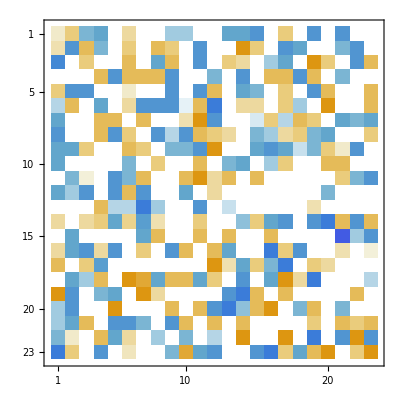

```mathematica
Map[MatrixPlot,{A.U1-UU2.ArrayFlatten[({{H11}, {R21}})]}]
```

```mathematica
{Q3,R32}= QRDecomposition[Q3];Q3=Q3ᵀ;
QQ2=ArrayFlatten[{{Q1,Q2}}];
QQ3=ArrayFlatten[{{Q1,Q2,Q3}}];
HH =ArrayFlatten[({{H11, H12}, {R21, H22}, {0, R32}})];
MatrixPlot[HH]
Norm[A.QQ2-QQ3.HH]
```

-Graphics-

1.59326×10^-15